# Roots

## Open Methods

Miles Hill

## Initialization

## Homework #1 ( 2015 )

### 6.19 Determine Frequency for Given Impedence

The figure shows a circuit with a resistor, an inductor, and a capacitor in parallel. Kirchoff’s rules can be used to express the impedance of the system as

1/Z=√(1/R^2+( ω C - 1/(ω L))^2)

where Z = impedance(Ω), and ω is the angular frequency.

Find ω that results in an impedance of 100Ω using the fzero function with initial guesses of 1 and 10^3 for the given parameters.
R,C,L = 225Ω, 0.6 10e-6 F, 0.5 H

The Mathematica equivalent of Matlab fzero will be one of the following: NSolve, FindRoot

#### Code

```mathematica
$Line=0;
```

```mathematica
(* Pure function return for given input values *)
Z[r_,c_,l_]:=(1/r^2+(# c-1/(# l))^2)^(-1/2)&
```

```mathematica
(* Solutions *)
NSolve[Z[225.,0.6 10^-6,0.5]@ω == 100 && 1.0<ω<1000.,ω,Reals][[1]];
```

```mathematica
FindRoot[ Z[225.0,.6 10^-6,0.5]@ω-100,{ω,1},AccuracyGoal->5,PrecisionGoal->6];
```

#### Output

```mathematica
DisplayColumn["Problem 6.19",{"NSolve","FindRoot"},{Out[2],Out[3]}]
```

NSolve
{ω→220.02}
FindRoot
{ω→220.02}Problem 6.19

### 6.21 Projectile Motion

The trajectory of an object defined by the xy-coordinates can be modeled by the given equation. Find the appropriate initial angle θ_0 if v_0=30 m/s and the horizontal distance is Δx =90m. Note that the initial elevation and final elevation are y_0,y_f=1.8,1.0 meters.

y=(tanθ_0)x-g/(2 v_0^2 cos^2 θ_0)x^2+y_0

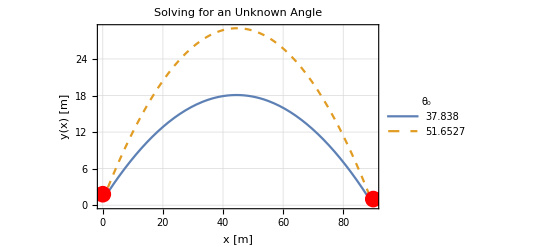

```mathematica
(* Constants *)
With[{v0=30.,x=90.,Δy=-0.8,g=9.8},
Block[{Traj,θ0,sol},
(* Equation to solve *)
Traj[d_]:=Tan[θ0]d-g/(2v0^2Cos[θ0]^2)d^2-Δy;
(* Restricting domain of Subscript[θ, 0] *)
sol=NSolve[Traj[x]==0 && 0.<θ0<Pi/2.,θ0];

(* Visual Output *)
Plot[Evaluate[{Traj[k]/.sol[[1]],
Traj[k]/.sol[[2]]
}],{k,0.,90.},

FrameLabel->{{"y(x) [m]",None},{"x [m]",None}},
PlotLabel->"Solving for an Unknown Angle",
PlotLegends->LineLegend[(θ0/.sol)(180./Pi),LegendLabel->"θ_0",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],
PlotStyle->{Default,Dashed},
PlotTheme->"Detailed",
Epilog->{Red,PointSize[0.03],Point[{0,1.8}],Point[{x,1.}]}
]

]]
```

### 6.29